```mathematica
region =ImplicitRegion[0≤x≤5&&0≤y≤1,{x,y}];
mesh = ToElementMesh[region, "MeshOrder"->2, "MaxCellMeasure"->0.5]
```

ElementMesh[{{0.,5.},{0.,1.}},{TriangleElement[<18>]}]

```mathematica
elms = mesh["MeshElements"][[1]][[1]]
```

{{1,5,13,17,18,19},{6,10,14,20,21,22},{5,9,13,23,24,18},{13,2,1,25,26,19},{14,5,6,27,28,22},{10,9,14,29,30,21},{6,7,10,31,32,20},{9,2,13,33,25,24},{7,8,15,34,35,36},{12,8,16,37,38,39},{3,4,16,40,41,42},{8,12,15,37,43,35},{11,7,15,44,36,45},{16,8,3,38,46,42},{11,15,12,45,43,47},{4,12,16,48,39,41},{7,11,10,44,49,32},{9,5,14,23,27,30}}

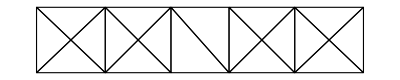

```mathematica
mesh["Wireframe"]
```

```mathematica
Export["coords.txt", mesh["Coordinates"]]
```

coords.txt